```mathematica
Quit[];
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.11 (2 Sep 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (6 Oct 2019)

by Thomas Hahn

```mathematica
(* Create my topologies. *)
(* 0 loops, 2 incoming legs, 2 outgoing legs.*)
topologies=CreateTopologies[0,2 -> 2];
_Hel=0;
Print[topologies];
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.gen

> $GenericMixing is OFF

generic model {DMsimp_s_spin1_vector} initialized

loading classes model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.mod

> 46 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 147 vertices

> 48 counterterms of order 1

classes model {DMsimp_s_spin1_vector} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

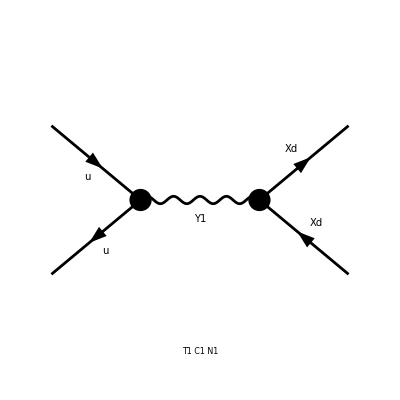

```mathematica
(* ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]} *)
diagvec=InsertFields[topologies,{F[7,{1}],-F[7,{1}]}->{F[13],-F[13]},InsertionLevel->{Classes},
Model->"DMsimp_s_spin1_vector",
GenericModel->"DMsimp_s_spin1_vector"];
Paint[diagvec];
```

```mathematica
ClearProcess[];
amplist = CreateFeynAmp[diagvec];
Print[amplist];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

FeynAmpList[Process→{{F[7,{1}],p1,0,{(2 Q)/3}},{-F[7,{1}],p2,0,{-(2 Q)/3}}}→{{F[13],k1,MXd,{}},{-F[13],k2,MXd,{}}},Model→{DMsimp_s_spin1_vector},GenericModel→{DMsimp_s_spin1_vector},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Classes==1,Number==1],Integral[],v̄[p2,0].(ⅈ gc75 ga[Lor1].(omSubscript[-])+ⅈ gc75 ga[Lor1].(omSubscript[+])).u[p1,0] ū[k1,MXd].(ⅈ gc76 ga[Lor2].(omSubscript[-])+ⅈ gc76 ga[Lor2].(omSubscript[+])).v[k2,MXd] g[Lor1,Lor2] 1/(-MY1^2+(k1+k2)^2)]]

```mathematica
amp=CalcFeynAmp[amplist,FermionChains->VA];
```

preparing FORM code in /Users/kpachal/fc-amp-3.frm

running FORM...

ok

```mathematica
(* Done with FeynArts! Time to pass the amplitude to FormCalc. *)
(* Squared matrix elements; evaluate *)
squared = SquaredME[amp];
Print[squared];
```

{FF[F1] FFC[F1] Mat[F1,F1],{FF[F1]→-gc75 gc76 Den[S,MY1^2],FFC[F1]→-(gc75Superscript[*]) (gc76Superscript[*]) Den[S,(MY1Superscript[*])^2]}}

```mathematica
(* SquaredME returns a list of {squared, squaredRules}, where we should later apply "squaredRules" to "squared". *)
ME = squared[[1]]//.squared[[2]]//.HelicityME[amp]//FullSimplify
```

> 1 helicity matrix elements

preparing FORM code in /Users/kpachal/fc-hel-3.frm

running FORM...

ok

1/2 gc75 gc76 (T^2+2 MXd^2 (MXd^2+S-T-U)+U^2) (gc75Superscript[*]) (gc76Superscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* Already in Mandelstam variables. *)
(* Now we need quantities we can recognize in the lab. *)
METheta = ME//.{U-> 2Mq^2 + 2MXd^2 - S - T,T-> Mq^2 + MXd^2 - (S - (S - 4Mq^2)^(1/2)(S - 4 MXd^2)^(1/2) CosTheta)/2,Den[p2_,m2_]:>1/(p2-m2)};
Print[METheta]
```

(gc75 gc76 ((Mq^2+MXd^2-S+1/2 (S-CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))^2+(Mq^2+MXd^2+1/2 (-S+CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))^2+2 MXd^2 (-2 Mq^2-MXd^2+2 S+1/2 (S-CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S))+1/2 (-S+CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))) (gc75Superscript[*]) (gc76Superscript[*]))/(2 (-MY1^2+S) (S-(MY1Superscript[*])^2))

```mathematica
(* This is our matrix element. Now to compute widths and cross sections. *)
(* Golden rule: dSigma/dOmega =(appx) 1/(64 Pi^2 S) |M^2| *)
dSigdOm = (64 Pi^2)^(-1) METheta/S
```

(gc75 gc76 ((Mq^2+MXd^2-S+1/2 (S-CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))^2+(Mq^2+MXd^2+1/2 (-S+CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))^2+2 MXd^2 (-2 Mq^2-MXd^2+2 S+1/2 (S-CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S))+1/2 (-S+CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))) (gc75Superscript[*]) (gc76Superscript[*]))/(128 π^2 S (-MY1^2+S) (S-(MY1Superscript[*])^2))

```mathematica
(* Total cross section: integral over 2 Pi d(CosTheta) from -1 to 1 *)
Sigma = 2 Pi Integrate[dSigdOm,{CosTheta,-1,1}]
```

(gc75 gc76 (3 Mq^4+4 Mq^2 (MXd^2-S)+S (2 MXd^2+S)) (gc75Superscript[*]) (gc76Superscript[*]))/(48 π S (-MY1^2+S) (S-(MY1Superscript[*])^2))

```mathematica
SigmaFinal = Integrate[Sigma,S]
```

(gc75 gc76 (gc75Superscript[*]) (gc76Superscript[*]) ((3 Mq^4+4 Mq^2 MXd^2) (MY1^2-(MY1Superscript[*])^2) Log[S]+(3 Mq^4+2 MXd^2 MY1^2+MY1^4+4 Mq^2 (MXd^2-MY1^2)) (MY1Superscript[*])^2 Log[-MY1^2+S]-MY1^2 (3 Mq^4+4 Mq^2 MXd^2+(-4 Mq^2+2 MXd^2) (MY1Superscript[*])^2+(MY1Superscript[*])^4) Log[S-(MY1Superscript[*])^2]))/(48 MY1^2 π (MY1Superscript[*])^2 (MY1^2-(MY1Superscript[*])^2))

```mathematica
LowerVal = SigmaFinal//. S->2MXd
```

(gc75 gc76 (gc75Superscript[*]) (gc76Superscript[*]) ((3 Mq^4+4 Mq^2 MXd^2) (MY1^2-(MY1Superscript[*])^2) Log[2 MXd]+(3 Mq^4+2 MXd^2 MY1^2+MY1^4+4 Mq^2 (MXd^2-MY1^2)) (MY1Superscript[*])^2 Log[2 MXd-MY1^2]-MY1^2 (3 Mq^4+4 Mq^2 MXd^2+(-4 Mq^2+2 MXd^2) (MY1Superscript[*])^2+(MY1Superscript[*])^4) Log[2 MXd-(MY1Superscript[*])^2]))/(48 MY1^2 π (MY1Superscript[*])^2 (MY1^2-(MY1Superscript[*])^2))

```mathematica
UpperVal = Limit[SigmaFinal,S->Infinity]
```

gc75 gc76 (gc75Superscript[*]) (gc76Superscript[*]) ∞